```mathematica
ClearAll[generateKeyWithPlot]
generateKeyWithPlot[seed_Integer]:=Module[{G=4 π^2,conv=1/(1.496*^8*365.25*24*3600),pos1,vel1,pos2,vel2,pos3,vel3,q2x,q2y,q3x,q3y,m1=1,m2=1,m3=1,eq,init,sol,traj1,traj2,traj3,timeSteps,positions,keyData,binaryKeyData,flattenedBinaryKey,randomSequence,key},(*Initial conditions*)pos1={0,0};
vel1={0,10}*conv;
SeedRandom[seed];
q2x=RandomReal[{5,20}];q2y=RandomReal[{0,10}];
pos2={q2x,q2y};vel2={-10,0}*conv;
q3x=RandomReal[{-10,0}];q3y=RandomReal[{5,20}];
pos3={q3x,q3y};vel3={0,0};
(*Differential equations*)eq={x1''[t]==G m2 (x2[t]-x1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (x3[t]-x1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,y1''[t]==G m2 (y2[t]-y1[t])/Norm[{x2[t]-x1[t],y2[t]-y1[t]}]^3+G m3 (y3[t]-y1[t])/Norm[{x3[t]-x1[t],y3[t]-y1[t]}]^3,x2''[t]==G m1 (x1[t]-x2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (x3[t]-x2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,y2''[t]==G m1 (y1[t]-y2[t])/Norm[{x1[t]-x2[t],y1[t]-y2[t]}]^3+G m3 (y3[t]-y2[t])/Norm[{x3[t]-x2[t],y3[t]-y2[t]}]^3,x3''[t]==G m1 (x1[t]-x3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (x2[t]-x3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3,y3''[t]==G m1 (y1[t]-y3[t])/Norm[{x1[t]-x3[t],y1[t]-y3[t]}]^3+G m2 (y2[t]-y3[t])/Norm[{x2[t]-x3[t],y2[t]-y3[t]}]^3};
(*Initial conditions for solver*)init={x1[0]==pos1[[1]],y1[0]==pos1[[2]],x2[0]==pos2[[1]],y2[0]==pos2[[2]],x3[0]==pos3[[1]],y3[0]==pos3[[2]],x1'[0]==vel1[[1]],y1'[0]==vel1[[2]],x2'[0]==vel2[[1]],y2'[0]==vel2[[2]],x3'[0]==vel3[[1]],y3'[0]==vel3[[2]]};
(*Solve system*)sol=NDSolve[{eq,init},{x1,y1,x2,y2,x3,y3},{t,0,100}];
(*Extract trajectories*)traj1={x1[t],y1[t]}/. sol;
traj2={x2[t],y2[t]}/. sol;
traj3={x3[t],y3[t]}/. sol;
(*Sample positions*)timeSteps=Range[0,100,0.1];
positions=Flatten[Table[{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]}/. sol,{t,timeSteps}],1];
(*Convert to binary*)keyData=Flatten[positions];
binaryKeyData=IntegerDigits[Round[Abs[keyData]*10^6],2,24];
flattenedBinaryKey=Flatten[binaryKeyData];
(*XOR with PRBS*)randomSequence=RandomInteger[{0,1},Length[flattenedBinaryKey]];
key=BitXor[flattenedBinaryKey,randomSequence];
(*Print info*)Print["Seed: ",seed];
Print["Key length: ",Length[key]];
Print["Counts: ",Counts[key]];
(*Plot trajectories*)Print[ParametricPlot[{traj1,traj2,traj3},{t,0,100},PlotLegends->{"Particle 1","Particle 2","Particle 3"},AxesLabel->{"x (au)","y (au)"},PlotRange->All,ImageSize->Large]];

(*Return key*)
key]
```

Seed: 12

Key length: 144144

Counts: <|0→71829,1→72315|>

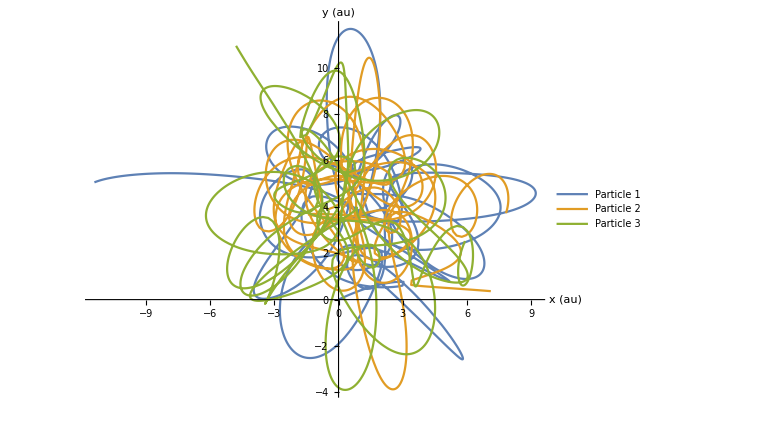

Seed: 22

Key length: 144144

Counts: <|1→72244,0→71900|>

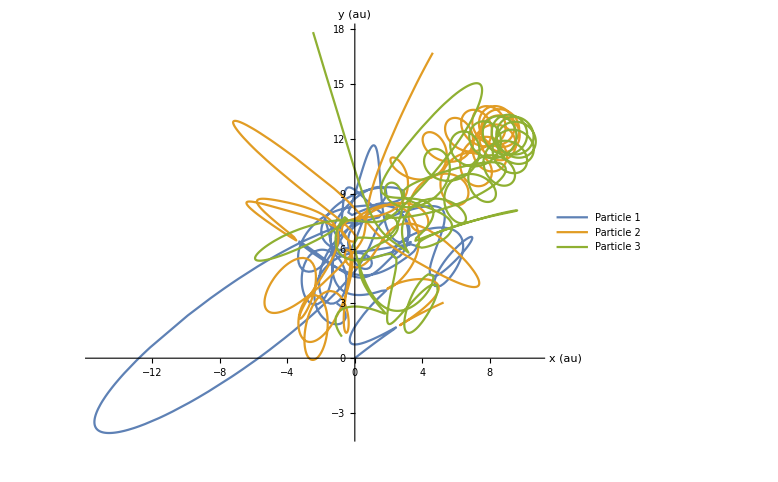

XOR key length: 144144

XOR key counts: <|1→71945,0→72199|>

```mathematica
key1=generateKeyWithPlot[12];
key2=generateKeyWithPlot[22];

len=Min[Length[key1],Length[key2]];
key=BitXor[key1[[;;len]],key2[[;;len]]];

Print["XOR key length: ",len];
Print["XOR key counts: ",Counts[key]];
```

```mathematica
(*SerialRandomnessTest*)
serialResult=N@ResourceFunction["SerialRandomnessTest"][key,"TestStatistic"];
serialPValue=N@ResourceFunction["SerialRandomnessTest"][key,"PValue"];
Print["Serial Randomness Test:"];
Print["  Test Statistic: ",serialResult];
Print["  P-Value: ",serialPValue];
If[serialPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ChiSquareRandomnessTest*)
chiSquareResult=N@ResourceFunction["ChiSquareRandomnessTest"][key,"TestStatistic"];
chiSquarePValue=N@ResourceFunction["ChiSquareRandomnessTest"][key,"PValue"];
Print["\nChi-Square Randomness Test:"];
Print["  Test Statistic: ",chiSquareResult];
Print["  P-Value: ",chiSquarePValue];
If[chiSquarePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*BinaryRunRandomnessTest*)
binaryRunResult=N@ResourceFunction["BinaryRunRandomnessTest"][key,"TestStatistic"];
binaryRunPValue=N@ResourceFunction["BinaryRunRandomnessTest"][key,"PValue"];
Print["\nBinary Run Randomness Test:"];
Print["  Test Statistic: ",binaryRunResult];
Print["  P-Value: ",binaryRunPValue];
If[binaryRunPValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];

(*ArcsineLawRandomnessTest*)
arcsineResult=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"TestStatistic"];
arcsinePValue=N@ResourceFunction["ArcsineLawRandomnessTest"][key,"PValue"]; (*Force numeric evaluation*)
Print["\nArcsine Law Randomness Test:"];
Print["  Test Statistic: ",arcsineResult];
Print["  P-Value: ",arcsinePValue];
If[arcsinePValue>0.05,Print["  Result: Good randomness (p-value > 0.05)"],Print["  Result: Bad randomness (p-value ≤ 0.05)"]];
```

Serial Randomness Test:

Test Statistic: 0.841303

P-Value: 0.643647

Result: Good randomness (p-value > 0.05)

Chi-Square Randomness Test:

Test Statistic: 0.44758

P-Value: 0.503486

Result: Good randomness (p-value > 0.05)

Binary Run Randomness Test:

Test Statistic: 71950.

P-Value: 0.521199

Result: Good randomness (p-value > 0.05)

Arcsine Law Randomness Test:

Test Statistic: 0.414259

P-Value: 0.890289

Result: Good randomness (p-value > 0.05)